# Genetic Algorithms Code - Background Data

## General Settings

### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(* Some unimportant error messages are switched off for future convenience *)
Off[ListInterpolation::inhr];
```

### Various Constants

```mathematica
(* Planck18 Values and other constants *)
obh2pl = 0.02237;
obh2plerr = 0.00015;
ompl = 0.3153;
omplerr = 0.0073;
σ8pl = 0.8111;
σ8err = 0.0060;
h0pl = 0.6736;
h0riess = 73.04/100;
Tcmb=2.7255;
c = 299792.458;
cH0=2997.92458;
ϵ0={-1,0,1};
errbandcol=GrayLevel[0.3,0.2];
```

## Genetic Algorithms Theory

### Genetic Algorithms Functions

```mathematica
polyx[x_]:=x
poly1x[x_]:=1+x
polyxtox[x_]:=x^x
grammarH={poly1x};
grammardL={polyx};
(* Expression length *)
length=4;
depth=4;
rang1={-1,1};
rang2={1,Length[grammardL]};
rang3={0,2};
rang4={0,4};
toursize=4;
selectionrate=0.3;
```

### Genetic Algorithms Basics

```mathematica
funcGA[x_,kid_,gram_]:=Sum[kid[[i,1]] (gram[[kid[[i,2]]]]@(kid[[i,3]]x))^kid[[i,4]],{i,1,length}]
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]};
mut=Which[rep[[2]]==1,RandomReal[rang1],rep[[2]]==2,RandomInteger[rang2],rep[[2]]==3,RandomReal[rang3],rep[[2]]==4,RandomInteger[rang4]];
ReplacePart[kid,rep->mut]]
cross[{kid1_,kid2_}]:=Module[{len},len=RandomInteger[{1,length-1}];
{Join[kid1[[1;;len]],kid2[[(len+1);;-1]]],Join[kid1[[(len+1);;-1]],kid2[[1;;len]]]}]

tournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[1,2]]
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[-1,2]]

GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomesdL,chromosomesH,t1,pigsdL,pigsH,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2];
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={};
chromosomesdL=Table[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomInteger[rang4]},{pop},{length}];
chromosomesH=Table[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomInteger[rang4]},{pop},{length}];
t1=AbsoluteTime[];
Do[
pigsH=(Sqrt[1+x funcGA[x,#,grammarH]^2] )&/@chromosomesH;
pigsdL=x(1+x funcGA[x,#,grammardL]^2)&/@chromosomesdL;
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[chi2totalGAm[pigsH[[j]],pigsdL[[j]]/(1+x)^2,pigsdL[[j]]],2,10^230],10^8,10^230],j},{j,1,Length[pigsdL]}],#1[[1]]>#2[[1]]&];AppendTo[bestfitperstep,{fitness[[1,1]],pigsH[[fitness[[1,2]]]],chromosomesH[[fitness[[1,2]]]],pigsdL[[fitness[[1,2]]]],chromosomesdL[[fitness[[1,2]]]]}];p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];Do[{chromosomesH[[p1[[jj,1]]]],chromosomesH[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomesH[[p2[[jj,1]]]], chromosomesH[[p2[[jj,2]]]]}],{chromosomesH[[p1[[jj,1]]]],chromosomesH[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];Do[{chromosomesH[[p1[[jj,1]]]],chromosomesH[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomesH[[p2[[jj,1]]]]],mutation[chromosomesH[[p2[[jj,2]]]]]},{chromosomesH[[p1[[jj,1]]]],chromosomesH[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];
Do[{chromosomesdL[[p1[[jj,1]]]],chromosomesdL[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomesdL[[p2[[jj,1]]]], chromosomesdL[[p2[[jj,2]]]]}],{chromosomesdL[[p1[[jj,1]]]],chromosomesdL[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];Do[{chromosomesdL[[p1[[jj,1]]]],chromosomesdL[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomesdL[[p2[[jj,1]]]]],mutation[chromosomesdL[[p2[[jj,2]]]]]},{chromosomesdL[[p1[[jj,1]]]],chromosomesdL[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];
prog`int++,{maxgens}];
If[verbose==True,
Print["Time taken: ",AbsoluteTime[]-t1," sec"];
Print["χ_min^2 = ",Abs[fitness[[1,1]]]];
Print["Best-fit function H(z) is: "];
Print[bestfitperstep[[-1,2]]];
Print["Best-fit function d_l(z) is: "];
Print[bestfitperstep[[-1,4]]];
Speak["The end"];];
bestfitperstep]
```

## Real Data Analysis - ΛCDM Model

### Basic Functions for the nCPL Model

```mathematica
(* See Eq. (2) of arxiv:9709112 *)
zeq[om_?NumberQ,h_?NumberQ]:=2.5*10^4 om h^2 (Tcmb/2.7)^-4;
aeq[om_?NumberQ,h_?NumberQ]:=1/(1+zeq[om,h]);
(* nCPL Dark Energy Model as a function of α *)
wcpl[a_,w0_,wa_,n_]:=w0+wa (1-a)^n
(* Subscript[f, DE](α) for nCPL Dark Energy Model *)
fcpl[a_,w0_,wa_,n_]:=a^(-3 (1+w0+wa)) ⅇ^(-3 wa HarmonicNumber[n]+3 a n wa HypergeometricPFQ[{1,1,1-n},{2,2},a]);Hcpl[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))fcpl[a,w0,wa,n]]
cs[a_?NumberQ,obh2_?NumberQ]:=c/√(3(1+(31500 obh2(Tcmb/2.7)^-4)a));
(* Redshift at decoupling - See Eqs. (66)-(68) of arxiv:0803.0547 *)
zcmb[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1048(1+0.00124(obh2)^-0.738)(1+((0.0783(obh2)^-0.238)/(1+39.5(obh2)^0.763))(om h^2)^(0.560/(1+21.1(obh2)^1.81)))
(* Drag redshift - see Eq. (4) of arxiv:9709112 *)
zdrag[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1291 ((om h^2)^0.251)/(1+0.659 (om h^2)^0.828)(1+(0.313(om h^2)^-0.419(1+0.607(om h^2)^0.674))(obh2)^(0.238(om h^2)^0.223))
rscpl[ze_,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=NIntegrate[cs[x,obh2]/(x^2Hcpl[x,om,w0,wa,n,h]),{x,10^-11,1/(1+ze[om,obh2,h])}]
Clear[DLsolcpl,DLcpl,dLcpl]
DLsolcpl[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(DLsolcpl[om,w0,wa,n,h]=NDSolve[{D[dLcpl[zz]/(1+zz),zz]==1/(Hcpl[1/(1+zz),om,w0,wa,n,h]/(100h)),dLcpl[0]==0},dLcpl,{zz,0,1300},MaxSteps->Infinity])
DLcpl[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(c/(100h)dLcpl[z]/.DLsolcpl[om,w0,wa,n,h])[[1]]//Chop
(* Angular diameter distance with curvature, see arxiv:0803.0547  *)
DAcpl[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=1/(1+z)^2 DLcpl[z,om,w0,wa,n,h]
baodacpl[z_,om_,w0_,wa_,n_,h_]:= DAcpl[z,om,w0,wa,n,h](rscpl[zdrag,ompl,obh2pl,-1,0,1,h0pl]/rscpl[zdrag,om,obh2pl,w0,wa,n,h]);
(* Dilation scale *)
Dvcpl[zbao_,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=((DLcpl[zbao,om,w0,wa,n,h]/(1+zbao))^2  (c*zbao)/Hcpl[1/(1+zbao),om,w0,wa,n,h])^(1/3)
(* BAO Subscript[d, z] ratio *)
dzcpl[zbao_,om_,obh2_,w0_,wa_,n_,h_]:=rscpl[zdrag,om,obh2,w0,wa,n,h]/Dvcpl[zbao,om,w0,wa,n,h]
(* DH "distance" *)
DHcpl[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=c/Hcpl[1/(1+z),om,w0,wa,n,h]
hzcpl[z_,om_,w0_,wa_,n_,h_]:=Hcpl[1/(1+z),om,w0,wa,n,h]
baodvcpl[z_,om_,w0_,wa_,n_,h_]:=rscpl[zdrag,ompl,obh2pl,-1,0,1,h0pl]/dzcpl[z,om,obh2pl,w0,wa,n,h];
(* DM "distance" ratio over rs(zd) *)
DMcpl[z_,om_,obh2_,w0_,wa_,n_,h_]:=((1+z)DAcpl[z,om,w0,wa,n,h])/rscpl[zdrag,om,obh2,w0,wa,n,h]
(* Scaled distance at recombination *)
Rcpl[om_,obh2_,w0_,wa_,n_,h_]:=√(om (100h)^2)DAcpl[zcmb[om,obh2,h],om,w0,wa,n,h](1+zcmb[om,obh2,h])/c
(* Angular scale of sound horizon at recombination *)
lacpl[om_,obh2_,w0_,wa_,n_,h_]:=π (DAcpl[zcmb[om,obh2,h],om,w0,wa,n,h](1+zcmb[om,obh2,h]))/(rscpl[zcmb,om,obh2,w0,wa,n,h])
```

### BAO data

#### Import the Various BAO Surveys

```mathematica
(* 6dFGs and WiggleZ BAO data - See arxiv:1605.02702 on page 6 *)
databao6dFWig={{0.106,0.336,0.015},{0.44,0.073,0.031},{0.6,0.0726,0.0164},{0.73,0.0592,0.0185}};
Cijbaoinv6dFWig=({{1/databao6dFWig[[1,3]]^2, 0, 0, 0}, {0, 1040.3, -807.5, 336.8}, {0, -807.5, 3720.3, -1551.9}, {0, 336.8, -1551.9, 2914.9}});
(* 6dFGs and WiggleZ BAO data, see arxiv:1605.02702 *)
vecbaocpl[om_,obh2_,w0_,wa_,n_,h_]:=Table[(databao6dFWig[[i,2]]-dzcpl[databao6dFWig[[i,1]],om,obh2,w0,wa,n,h]),{i,1,Length[databao6dFWig]}];
chi2bao6dFWig[om_,obh2_,w0_,wa_,n_,h_]:=vecbaocpl[om,obh2,w0,wa,n,h].Cijbaoinv6dFWig.vecbaocpl[om,obh2,w0,wa,n,h]
```

```mathematica
(* BAO measurement for MGS and eBOSS ELG is DV/rs=1/dz! (2007.08991) *)
dataMGSELG={{0.15,4.465666824,0.1681350461},{0.85,18.33,(0.57+0.62)/2}};
chi2MGSELG[om_,obh2_,w0_,wa_,n_,h_]:=Sum[((dataMGSELG[[i,2]]-1/dzcpl[dataMGSELG[[i,1]],om,obh2,w0,wa,n,h])/dataMGSELG[[i,3]])^2,{i,1,Length[dataMGSELG]}]
```

```mathematica
(* BAO measurements from DES 3yr (2107.04646) is DM=(1+z)*Da/rs! *)
dataDES3={{0.835,18.92,0.51}};
chi2DES[om_,obh2_,w0_,wa_,n_,h_]:=((dataDES3[[1,2]]-DMcpl[dataDES3[[1,1]],om,obh2,w0,wa,n,h])/dataDES3[[1,3]])^2
```

```mathematica
(* BAO measurements eBOSS - LRG (2007.08991) *)
dataLRG=Import["./data/sdss_DR16_LRG_v12_bao.txt","Table"];
dataLRGCijinv=Inverse[Import["./data/sdss_DR16_LRG_v12_bao_covtot.txt","Table"]];
vecLRG[om_,obh2_,w0_,wa_,n_,h_]:={dataLRG[[1,2]]-DMcpl[dataLRG[[1,1]],om,obh2,w0,wa,n,h],dataLRG[[2,2]]-DHcpl[dataLRG[[2,1]],om,w0,wa,n,h]/rscpl[zdrag,om,obh2,w0,wa,n,h]}
chi2LRG[om_,obh2_,w0_,wa_,n_,h_]:=vecLRG[om,obh2,w0,wa,n,h].dataLRGCijinv.vecLRG[om,obh2,w0,wa,n,h]
```

```mathematica
(* BAO measurements eBOSS - Quasars (2007.08991) *)
dataQSO=Import["./data/sdss_DR16_QSO_BAO_DMDH.txt","Table"];
dataQSOCijinv=Inverse[Import["./data/sdss_DR16_QSO_BAO_DMDH_covtot.txt","Table"]];
vecQSO[om_,obh2_,w0_,wa_,n_,h_]:={dataQSO[[1,2]]-DMcpl[dataQSO[[1,1]],om,obh2,w0,wa,n,h],dataQSO[[2,2]]-DHcpl[dataQSO[[2,1]],om,w0,wa,n,h]/rscpl[zdrag,om,obh2,w0,wa,n,h]}
chi2QSO[om_,obh2_,w0_,wa_,n_,h_]:=vecQSO[om,obh2,w0,wa,n,h].dataQSOCijinv.vecQSO[om,obh2,w0,wa,n,h]
```

```mathematica
(* BAO measurements from Lya are {DH/rs,DM/rs}! *)
(* Joint Lya auto+cross correlation (with QSOs) measurement from 2007.08995, see Eq. (43) *)
dataLya={{2.334,8.99,√(0.2^2+0.38^2)},{2.334,37.5,√(1.2^2+2.5^2)}};
ρLya=-0.45;
CijLyainv=Inverse[{{dataLya[[1,3]]^2,ρLya dataLya[[1,3]] dataLya[[2,3]]},{ρLya dataLya[[1,3]] dataLya[[2,3]],dataLya[[2,3]]^2}}];
vecLya[om_,obh2_,w0_,wa_,n_,h_]:={dataLya[[1,2]]-DHcpl[dataLya[[1,1]],om,w0,wa,n,h]/rscpl[zdrag,om,obh2,w0,wa,n,h],dataLya[[2,2]]-DMcpl[dataLya[[2,1]],om,obh2,w0,wa,n,h]};
chi2Lya[om_,obh2_,w0_,wa_,n_,h_]:=vecLya[om,obh2,w0,wa,n,h].CijLyainv.vecLya[om,obh2,w0,wa,n,h]
```

```mathematica
(* eBOSS Galaxy samples DR12, Table 3 in 2007.08991 *)
dataDR12=Import["./data/sdss_DR12_LRG_BAO_DMDH.txt","Table"];
dataDR12Cijinv=Inverse[Import["./data/sdss_DR12_LRG_BAO_DMDH_covtot.txt","Table"]];
vecDR12[om_,obh2_,w0_,wa_,n_,h_]:={dataDR12[[1,2]]-DMcpl[dataDR12[[1,1]],om,obh2,w0,wa,n,h],
dataDR12[[2,2]]-DHcpl[dataDR12[[2,1]],om,w0,wa,n,h]/rscpl[zdrag,om,obh2,w0,wa,n,h],
dataDR12[[3,2]]-DMcpl[dataDR12[[3,1]],om,obh2,w0,wa,n,h],dataDR12[[4,2]]-DHcpl[dataDR12[[4,1]],om,w0,wa,n,h]/rscpl[zdrag,om,obh2,w0,wa,n,h]}
chi2DR12[om_,obh2_,w0_,wa_,n_,h_]:=vecDR12[om,obh2,w0,wa,n,h].dataDR12Cijinv.vecDR12[om,obh2,w0,wa,n,h]
```

#### Total χ^2 of BAO

```mathematica
(* Total BAO χ^2 function *)
chi2bao[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=chi2bao6dFWig[om,obh2,w0,wa,n,h]+chi2MGSELG[om,obh2,w0,wa,n,h]+chi2DES[om,obh2,w0,wa,n,h]+chi2LRG[om,obh2,w0,wa,n,h]+chi2QSO[om,obh2,w0,wa,n,h]+chi2Lya[om,obh2,w0,wa,n,h]+chi2DR12[om,obh2,w0,wa,n,h]
ndatBAO=Length[databao6dFWig]+Length[dataMGSELG]+Length[dataLRG]+Length[dataQSO]+Length[dataLya]+Length[dataDR12]+Length[dataDES3]
```

17

#### BAO Data - Maximum Likelihood Method for ΛCDM

```mathematica
minBAO=FindMinimum[chi2bao[om,obh2pl,-1,0,1,h],{om,0.3,0.31},{h,0.67,0.68}];
ombfBAO=minBAO[[2,1,2]];
hbfBAO=minBAO[[2,2,2]];
chifunBAO=ListInterpolation[ParallelTable[chi2bao[om,obh2pl,-1,0,1,h],{om,ombfBAO-0.02,ombfBAO+0.02,0.02},{h,hbfBAO-0.02,hbfBAO+0.02,0.02},DistributedContexts->Automatic],{{ombfBAO-0.02,ombfBAO+0.02},{hbfBAO-0.02,hbfBAO+0.02}}];
(* Params that we want to calculate the errors *)
paramsBAO={om,h};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
FijBAO=1/2 Table[D[chifunBAO[om,h],paramsBAO[[p]],paramsBAO[[d]]]/.minBAO[[2]],{p,1,Length[paramsBAO]},{d,1,Length[paramsBAO]}];
cijBAO=Inverse[FijBAO];
errorsBAO=Sqrt[Diagonal[cijBAO]];
Print["The best fit parameter for Ω_(0  m) and h is: Ω_(0  m)=",ombfBAO,"±",errorsBAO[[1]]," and h=",hbfBAO,"±",errorsBAO[[2]]," with a χ^2 value: χ^2=",minBAO[[1]]]
```

The best fit parameter for Ω_(0  m) and h is: Ω_(0  m)=0.308017±0.0247688 and h=0.650236±0.0126277 with a χ^2 value: χ^2=13.7

### SnIa Data

#### Import the Pantheon Data

```mathematica
dataPanth=Import["./data/lcparam_full_long_zhel.txt","Table"];
ndatPanth=Length[dataPanth]-1;
Dij0=Import["./data/sys_full_long.txt","List"];
Dij=Partition[Dij0[[2;;-1]],{Dij0[[1]]}];
Covstat=DiagonalMatrix[dataPanth[[All,6]][[2;;-1]]^2];
Covsys=Dij;
Cijtot=Covsys+Covstat;
InvCovTotal=Inverse[Cijtot];
InvCovstat=Inverse[Covstat];
Id=ConstantArray[1,ndatPanth];
```

#### Total χ^2 of Pantheon

```mathematica
(* χ^2 Formula *)
chi2Panthmarge[data_,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=Module[{Δm,A,B,Ee},
Δm=Table[data[[1+i,5]]-(5 Log10[(1+data[[1+i,3]])/(1+data[[1+i,2]])DLcpl[data[[1+i,2]],om,w0,wa,n,h]]+25),{i,1,ndatPanth}];
A=Δm.InvCovTotal.Δm;
B=Δm.InvCovTotal.Id;
Ee=Id.InvCovTotal.Id;
A+Log[Ee/(2Pi)]-B^2/Ee]
ndatPanth
```

1048

#### Pantheon Data - Maximum Likelihood Method for ΛCDM

```mathematica
minPanth=FindMinimum[chi2Panthmarge[dataPanth,om,-1,0,1,h0pl],{om,0.29,0.291}];
ombfPanth=minPanth[[2,1,2]];
chifunPanth=ListInterpolation[ParallelTable[chi2Panthmarge[dataPanth,om,-1,0,1,0.67],{om,ombfPanth-0.02,ombfPanth+0.02,0.02},DistributedContexts->Automatic],{{ombfPanth-0.02,ombfPanth+0.02}}];
(* Params that we want to calculate the errors *)
paramsPanth={om};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
FijPanth=1/2 Table[D[chifunPanth[om],paramsPanth[[p]],paramsPanth[[d]]]/.minPanth[[2]],{p,1,Length[paramsPanth]},{d,1,Length[paramsPanth]}];
cijPanth=Inverse[FijPanth];
errorsPanth=Sqrt[Diagonal[cijPanth]];
Print["The best fit parameter for Ω_(0  m) is: Ω_(0  m)=",ombfPanth,"±",errorsPanth[[1]]," with a χ^2 value: χ^2=",minPanth[[1]]]
```

The best fit parameter for Ω_(0  m) is: Ω_(0  m)=0.298875±0.0219023 with a χ^2 value: χ^2=1034.73

### CC Data

#### Import the CC Data

```mathematica
dataHz=Import["./data/cc_data.txt","Table"];
ndatHz=Length[dataHz]
```

39

#### Total χ^2 of CC

```mathematica
(* χ^2 Formula *)
chi2CC[data_,om_,w0_,wa_,n_,h_]:=Sum[((data[[i,2]]-Hcpl[1/(1+data[[i,1]]),om,w0,wa,n,h])/data[[i,3]])^2,{i,1,ndatHz}]
```

#### CC Data - Maximum Likelihood Method for ΛCDM

```mathematica
minCC=FindMinimum[chi2CC[dataHz,om,-1,0,1,h],{om,0.29,0.30},{h,0.67,0.68}];
ombfCC=minCC[[2,1,2]];
hbfCC=minCC[[2,2,2]];
chifunCC=ListInterpolation[ParallelTable[chi2CC[dataHz,om,-1,0,1,h],{om,ombfCC-0.02,ombfCC+0.02,0.02},{h,hbfCC-0.02,hbfCC+0.02,0.02},DistributedContexts->Automatic],{{ombfCC-0.02,ombfCC+0.02},{hbfCC-0.02,hbfCC+0.02}}];
(* Params that we want to calculate the errors *)
paramsCC={om,h};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
FijCC=1/2 Table[D[chifunCC[om,h],paramsCC[[p]],paramsCC[[d]]]/.minCC[[2]],{p,1,Length[paramsCC]},{d,1,Length[paramsCC]}];
cijCC=Inverse[FijCC];
errorsCC=Sqrt[Diagonal[cijCC]];
Print["The best fit parameter for Ω_(0  m) and h is: Ω_(0  m)=",ombfCC,"±",errorsCC[[1]]," and h=",hbfCC,"±",errorsCC[[2]]," with a χ^2 value: χ^2=",minCC[[1]]]
```

The best fit parameter for Ω_(0  m) and h is: Ω_(0  m)=0.25845±0.0288577 and h=0.703313±0.0229167 with a χ^2 value: χ^2=19.6244

### Total χ^2 - Maximum Likelihood Method for ΛCDM

```mathematica
chi2total[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:= chi2bao[om,obh2,w0,wa,n,h]+chi2Panthmarge[dataPanth,om,w0,wa,n,h]+chi2CC[dataHz,om,w0,wa,n,h]
ndatotal=ndatBAO+ndatPanth+ndatHz
```

1104

```mathematica
mintotal=FindMinimum[chi2total[om,obh2pl,-1,0,1,h],{om,0.29,0.30},{h,0.67,0.68}];ombftotal=mintotal[[2,1,2]];
hbftotal=mintotal[[2,2,2]];
chifuntotal=ListInterpolation[ParallelTable[chi2total[om,obh2pl,-1,0,1,h],{om,ombftotal-0.02,ombftotal+0.02,0.02},{h,hbftotal-0.02,hbftotal+0.02,0.02},DistributedContexts->Automatic],{{ombftotal-0.02,ombftotal+0.02},{hbftotal-0.02,hbftotal+0.02}}];
(* Params that we want to calculate the errors *)
paramstotal={om,h};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
Fijtotal=1/2 Table[D[chifuntotal[om,h],paramstotal[[p]],paramstotal[[d]]]/.mintotal[[2]],{p,1,Length[paramstotal]},{d,1,Length[paramstotal]}];
cijtotal=Inverse[Fijtotal];
errorstotal=Sqrt[Diagonal[cijtotal]];
Print["The best fit parameter for Ω_(0  m) and h is: Ω_(0  m)=",ombftotal,"±",errorstotal[[1]]," and h=",hbftotal,"±",errorstotal[[2]]," with a χ^2 value: χ^2=",mintotal[[1]]]
```

The best fit parameter for Ω_(0  m) and h is: Ω_(0  m)=0.313312±0.0101147 and h=0.658687±0.00664802 with a χ^2 value: χ^2=1072.72

## Genetic Algorithms

### Genetic Algorithms Theory

#### Some GA Functions

```mathematica
(* In what follows HGA and DA are dimensionless *)
DvGA[z_,HGA_,DA_,h_]:=cH0/h(((1+z)DA )^2 z/HGA)^(1/3)
(* Hubble distance *)
DHGA[HGA_,h_]:=cH0/h 1/HGA
(* dz GA distance *)
dzGA[z_,HGA_,DA_,h_,rs_]:=rs/DvGA[z,HGA,DA,h]
(* DM "distance" ratio over rs(zd) *)
DMGA[z_,DA_,h_,rs_]:=cH0/h((1+z)DA)/rs
```

#### Specific χ^2 Functions - GA

```mathematica
(* 6dFGs and WiggleZ BAO data, see 1605.02702 *)
chi2bao6dFWigGA[HGA_,DA_,h_,rs_]:=
Module[{Hx,DAx,vecbaoGA},
Hx=HGA/.x->databao6dFWig[[All,1]];
DAx=DA/.x->databao6dFWig[[All,1]];vecbaoGA=Table[(databao6dFWig[[i,2]]-dzGA[databao6dFWig[[i,1]],Hx[[i]],DAx[[i]],h,rs]),{i,1,Length[databao6dFWig]}];vecbaoGA.Cijbaoinv6dFWig.vecbaoGA]
```

```mathematica
(* BAO measurement for MGS and eBOSS ELG is DV/rs=1/dz! (2007.08991) *)
chi2MGSELGGA[HGA_,DA_,h_,rs_]:=Module[{Hx,DAx},
Hx=HGA/.x->dataMGSELG[[All,1]];
DAx=DA/.x->dataMGSELG[[All,1]];Sum[((dataMGSELG[[i,2]]-1/dzGA[dataMGSELG[[i,1]],Hx[[i]],DAx[[i]],h,rs])/dataMGSELG[[i,3]])^2,{i,1,Length[dataMGSELG]}]]
```

```mathematica
(* BAO measurements from DES 3yr (2107.04646) is DM=(1+z)*Da/rs! *)
chi2DESGA[DA_,h_,rs_]:=
Module[{DAx},DAx=DA/.x->dataDES3[[1,1]];((dataDES3[[1,2]]-DMGA[dataDES3[[1,1]],DAx,h,rs])/dataDES3[[1,3]])^2]
```

```mathematica
(* BAO measurements eBOSS - LRG (2007.08991) *)
chi2LRGGA[HGA_,DA_,h_,rs_]:=Module[{Hx,DAx,vecLRGGA},
Hx=HGA/.x->dataLRG[[1,1]];
DAx=DA/.x->dataLRG[[1,1]];
vecLRGGA={dataLRG[[1,2]]-DMGA[dataLRG[[1,1]],DAx,h,rs],dataLRG[[2,2]]-DHGA[Hx,h]/rs};
vecLRGGA.dataLRGCijinv.vecLRGGA]
```

```mathematica
(* BAO measurements eBOSS - Quasars (2007.08991) *)
chi2QSOGA[HGA_,DA_,h_,rs_]:=Module[{Hx,DAx,vecQSOGA},
Hx=HGA/.x->dataQSO[[1,1]];
DAx=DA/.x->dataQSO[[1,1]];
vecQSOGA={dataQSO[[1,2]]-DMGA[dataQSO[[1,1]],DAx,h,rs],dataQSO[[2,2]]-DHGA[Hx,h]/rs};
vecQSOGA.dataQSOCijinv.vecQSOGA]
```

```mathematica
(* BAO measurements from Lya are {DH/rs,DM/rs}! *)
(* Joint Lya auto+cross correlation (with QSOs) measurement from 2007.08995, see Eq. (43) *)
chi2LyaGA[HGA_,DA_,h_,rs_]:=Module[{Hx,DAx,vecLyaGA},
Hx=HGA/.x->dataLya[[1,1]];
DAx=DA/.x->dataLya[[1,1]];
vecLyaGA={dataLya[[1,2]]-DHGA[Hx,h]/rs,dataLya[[2,2]]-DMGA[dataLya[[1,1]],DAx,h,rs]};
vecLyaGA.CijLyainv.vecLyaGA]
```

```mathematica
(* eBOSS Galaxy samples DR12, Table 3 in 2007.08991 *)
chi2DR12GA[HGA_,DA_,h_,rs_]:=Module[{Hx,DAx,vecDR12GA},
Hx=HGA/.x->dataDR12[[1;;-1;;2,1]];
DAx=DA/.x->dataDR12[[1;;-1;;2,1]];
vecDR12GA={dataDR12[[1,2]]-DMGA[dataDR12[[1,1]],DAx[[1]],h,rs],dataDR12[[2,2]]-DHGA[Hx[[1]],h]/rs,dataDR12[[3,2]]-DMGA[dataDR12[[3,1]],DAx[[2]],h,rs],dataDR12[[4,2]]-DHGA[Hx[[2]],h]/rs};
vecDR12GA.dataDR12Cijinv.vecDR12GA]
```

```mathematica
(* Total BAO χ^2 *)
chi2baoGA[rs_,HGA_,DA_,h_]:=chi2bao6dFWigGA[HGA,DA,h,rs]+chi2MGSELGGA[HGA,DA,h,rs]+chi2DESGA[DA,h,rs]+chi2LRGGA[HGA,DA,h,rs]+chi2QSOGA[HGA,DA,h,rs]+chi2LyaGA[HGA,DA,h,rs]+chi2DR12GA[HGA,DA,h,rs]
```

```mathematica
rsfid=rscpl[zdrag,ompl,obh2pl,-1,0,1,h0pl];
(* Total BAO chi^2 // numerically minmimized over rsh, where rsh=Subscript[r, s]*h, so that Subscript[r, s]=rsh Mpc/h! *)
chi2baoGAm[HGA_,DA_]:=Module[{temp},temp=chi2baoGA[h0pl rsfid,HGA,DA,1];If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,FindMinimum[chi2baoGA[rsh,HGA,DA,1],{rsh,h0pl rsfid,1.01h0pl rsfid},MaxIterations->1000][[1]],1. 10^230]]
```

```mathematica
(* χ^2 for SnIa *)
chi2PanthGAm[f_]:=Module[{temp,ft,Δm,A,B,Ee},
ft=(f/.x->#)&;
Δm=Table[dataPanth[[1+i,5]]-(5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])ft[dataPanth[[1+i,2]]]]+25),{i,1,ndatPanth}];
A=Δm.InvCovTotal.Δm;
B=Δm.InvCovTotal.Id;
Ee=Id.InvCovTotal.Id;
temp=A+Log[Ee/(2Pi)]-B^2/Ee;If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]]
```

```mathematica
(* χ^2 for CC *)
chi2CCGAm[f_]:=Module[{temp,A,B,Γ,ft},ft=(f/.x->#)&;
A=Sum[(dataHz[[ii,2]]/dataHz[[ii,3]])^2,{ii,1,Length[dataHz]}];
B=Sum[((dataHz[[ii,2]]*ft[dataHz[[ii,1]]])/dataHz[[ii,3]]^2),{ii,1,Length[dataHz]}];
Γ=Sum[(ft[dataHz[[ii,1]]]/dataHz[[ii,3]])^2,{ii,1,Length[dataHz]}];
temp=A-B^2/Γ;
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]]
```

#### Total χ^2 - GA

```mathematica
chi2totalGAm[HGA_,DA_,DL_]:=chi2baoGAm[HGA,DA]+chi2PanthGAm[DL]+chi2CCGAm[HGA]
```

### Genetic Algorithms Calculations

#### Main Loop

```mathematica
t1=AbsoluteTime[];
generations=1500;
samples=10;
prog`int=0;prog`pop=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
ProgressIndicator[Dynamic[prog`pop],{0,samples}]
(* {randomseed, maxgens, population, crossoverrate, mutationrate, verbose (True/False)} *)
Do[GApop[jj]=GAevo[123jj,generations,100,0.75,0.25,False];prog`pop++;prog`int=0;,{jj,1,samples}];
Print["Time Taken: ",(AbsoluteTime[]-t1)/60," minutes"]
```

Time Taken: 86.64918481 minutes

#### Derived Results

```mathematica
(* The results are presented in the form {Subscript[d, L](x), H(x), # of sample} *)
fGAdistro=Table[{GApop[jj][[-1,2]],GApop[jj][[-1,4]],jj},{jj,1,samples}]
chi2tab=Table[{GApop[jj][[-1,1]]//Abs,jj},{jj,1,samples}]//Sort
Select[chi2tab,#[[1]]<mintotal[[1]]&]
```

{{√(1+x (-0.827154-0.222153 (1+1.9873 x))^2),x (1+x (0.790078-0.0466524 x^2)^2),1},{√(1+(-0.364308+0.106594 (1+0.0425271 x)^4-0.495214 (1+0.445856 x)-0.275096 (1+0.918303 x))^2 x),x (1+x (0.835663-0.0859107 x-0.0123098 x^2)^2),2},{√(1+(-0.0513009 (1+0.214414 x)-0.63701 (1+0.36626 x)-0.250652 (1+0.57456 x)-0.0943356 (1+0.607635 x))^2 x),x (1+(0.870506-0.128854 x)^2 x),3},{√(1+x (0.642129+0.408473 (1+1.08285 x))^2),x (1+x (0.787817-0.0455802 x^2)^2),4},{√(1+(0.276698+0.881989 (1+0.0835789 x)^4)^2 x),x (1+x (-0.783672+0.042301 x^2)^2),5},{√(1+(0.257623 (1+0.0889883 x)^4+0.570716 (1+0.333747 x)+0.285358 (1+0.405834 x))^2 x),x (1+x (-0.84228+0.112097 x+0.000286226 x^4)^2),6},{√(1+x (-0.899988+0.262038 (1+0.153278 x)^3-0.38198 (1+1.619 x))^2),x (1+(0.871835-0.12885 x)^2 x),7},{√(1+x (0.0730002-0.919788 (1+0.0176447 x)^2-0.0844162 (1+1.40586 x)-0.145595 (1+1.96406 x))^2),x (1+x (-0.78433+0.0420332 x^2)^2),8},{√(1+x (-0.827852-0.014413 (1+0.631777 x)-0.224303 (1+1.90924 x))^2),x (1+(-0.850462+0.116844 x)^2 x),9},{√(1+x (-1.00034 (1+0.00696071 x)^4+0.346774 (1+0.833371 x)-0.395492 (1+1.77113 x))^2),x (1+(-0.863844+0.124809 x)^2 x),10}}

{{1065.87,7},{1066.01,10},{1066.17,9},{1066.23,3},{1066.87,2},{1067.37,6},{1072.19,1},{1072.2,4},{1072.76,8},{1074.41,5}}

{{1065.87,7},{1066.01,10},{1066.17,9},{1066.23,3},{1066.87,2},{1067.37,6},{1072.19,1},{1072.2,4}}

```mathematica
Rasterize[ListLogLogPlot[Table[GApop[jj][[All,1]]//Abs,{jj,1,samples}],Joined->True,PlotRange->{700,6000},Frame->True,FrameStyle->Black,Epilog->{Dashed,Line[{{0.1,mintotal[[1]]},{generations,mintotal[[1]]}}//Log]},FrameLabel->{"N","χ^2(N)"},FrameStyle->Black,BaseStyle->FontSize->14,PlotLegends->Automatic],ImageSize->700]
```

-Graphics-

```mathematica
fGAdistro[[7]]
chi2tab[[7]]
```

{√(1+x (-0.899988+0.262038 (1+0.153278 x)^3-0.38198 (1+1.619 x))^2),x (1+(0.871835-0.12885 x)^2 x),7}

{1065.87,7}

### Comparison with ΛCDM

#### H(z) Plot

```mathematica
H0marg[f_]:=Module[{temp,B,Γ,ft},ft=(f/.x->#)&;
B=Sum[((dataHz[[ii,2]]*ft[dataHz[[ii,1]]])/dataHz[[ii,3]]^2),{ii,1,Length[dataHz]}];
Γ=Sum[(ft[dataHz[[ii,1]]]/dataHz[[ii,3]])^2,{ii,1,Length[dataHz]}];;
temp=B/Γ;
If[MatchQ[temp,_Real]&&$MinNumber<temp<$MaxNumber,temp,1. 10^230]]
```

```mathematica
Hga[x_]:=√(1+x (-0.8999883844902956+0.2620381909322407 (1+0.15327819800211584 x)^3-0.381979946511561 (1+1.6189955164319452 x))^2);
H0GA=H0marg[Hga[x]]
HGA[x_]:=H0GA√(1+x (-0.8999883844902956+0.2620381909322407 (1+0.15327819800211584 x)^3-0.381979946511561 (1+1.6189955164319452 x))^2);
```

67.17

```mathematica
dH[z_,a1_,a2_,a3_,a4_]:=a1+a2 z+a3 z^2+a4 z^4
```

```mathematica
chi2CI[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ,a4_?NumericQ]:=Module[{CI},CI=Table[1/2 (Erf[1/(√2 dataHz[[i,3]])(H0GA dH[dataHz[[i,1]],a1,a2,a3,a4]+HGA[dataHz[[i,1]]]-dataHz[[i,2]])]+Erf[1/(√2 dataHz[[i,3]])(H0GA dH[dataHz[[i,1]],a1,a2,a3,a4]-HGA[dataHz[[i,1]]]+dataHz[[i,2]])]),{i,1,Length[dataHz]}];
Sum[(CI[[i]]-Erf[1/(√2)])^2,{i,1,Length[dataHz]}]]
```

```mathematica
chi2ga[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ,a4_?NumericQ]:=chi2CCGAm[HGA[x]+H0GA dH[x,a1,a2,a3,a4]]
```

```mathematica
chi2totHz[a1_,a2_,a3_,a4_]:=chi2CI[a1,a2,a3,a4]+chi2ga[a1,a2,a3,a4]
```

```mathematica
fminerrHtot2=FindMinimum[chi2totHz[a1,a2,0,0],{a1,0.11,0.111},{a2,0.11,0.111},MaxIterations->500]
```

{20.8897,{a1→0.181938,a2→0.202018}}

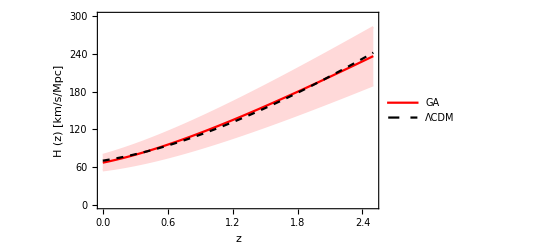

```mathematica
pltHz=Plot[{HGA[z]+H0GA dH[z,a1,a2,0,0]ϵ0/.fminerrHtot2[[2]]//Evaluate,Hcpl[1/(1+z),ombfCC,-1,0,1,hbfCC]},{z,0,2.5},PlotStyle->{LightRed,Red,LightRed,{Dashed,Black}},Filling->{1->{{3},LightRed}},Frame->True,FrameLabel->{"z","H (z) [km/s/Mpc]"},FrameStyle->Black,BaseStyle->FontSize->16,PlotRange->{0,300},PlotLegends->Placed[LineLegend[{Red,{Dashed,Black}},{"GA","ΛCDM"}],Scaled[{0.8,0.2}]],Axes->None]
```

```mathematica
Export[NotebookDirectory[]<>"Hzplot.pdf",pltHz,ImageResolution->600];
```

#### d_L (z) Plot

```mathematica
dLGA[x_]:=x (1+(0.8718351321839224-0.12885030729521135 x)^2 x);
```

```mathematica
Clear[δdL]
δdL[x_,a1_,a2_,a3_,a4_]:=x^2(a1+a2 x/(1+x)+a3 (x/(1+x))^2+a4 (x/(1+x))^3)
```

```mathematica
M0par[f_]:=Module[{temp,ft,Δm,A,B,Ee},
ft=(f/.x->#)&;
Δm=Table[dataPanth[[1+i,5]]-(5 Log10[(1+dataPanth[[1+i,3]])/(1+dataPanth[[1+i,2]])ft[dataPanth[[1+i,2]]]]+25),{i,1,ndatPanth}];
A=Δm.InvCovTotal.Δm;
B=Δm.InvCovTotal.Id;
Ee=Id.InvCovTotal.Id;
B/Ee]
```

```mathematica
M0=M0par[dLGA[x]];
```

```mathematica
Dij=-CholeskyDecomposition[(InvCovTotal+Transpose[InvCovTotal])/2];
yj=dataPanth[[2;;-1,5]];

fbfj=Table[M0+5 Log10[((1+dataPanth⟦1+j,3⟧) dLGA[dataPanth⟦1+j,2⟧])/(1+dataPanth⟦1+j,2⟧)]+25,{j,1,ndatPanth}];
```

```mathematica
chi2confSnIa[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ,a4_?NumericQ]:=Module[{δfj,vec1,vec2,conf},
δfj=Table[5/Log[10] δdL[dataPanth⟦1+j,2⟧,a1,a2,a3,a4]/dLGA[dataPanth⟦1+j,2⟧],{j,1,ndatPanth}];
vec1=-Dij.(+yj-fbfj+δfj);
vec2=-Dij.(-yj+fbfj+δfj);
conf=Table[1/2 (Erf[vec1[[i]]/(√2) ]+Erf[vec2[[i]]/(√2) ]),{i,1,ndatPanth}];
Sum[(conf[[k]]-Erf[1/(√2)])^2,{k,1,ndatPanth}]]
```

```mathematica
chi2totdL[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ,a4_?NumericQ]:=chi2PanthGAm[dLGA[x]+δdL[x,a1,a2,a3,a4]]+chi2confSnIa[a1,a2,a3,a4]
```

```mathematica
fmindLerr=FindMinimum[chi2totdL[a1,a2,a3,0],{a1,0.10,0.11},{a2,0.10,0.11},{a3,0.10,0.11}]
```

{1159.6,{a1→0.928448,a2→-3.21396,a3→3.03401}}

```mathematica
fmindLerr={1159.6033846220112,{a1->0.9284476692397967,a2->-3.2139585518000273,a3->3.034013971574597}};
```

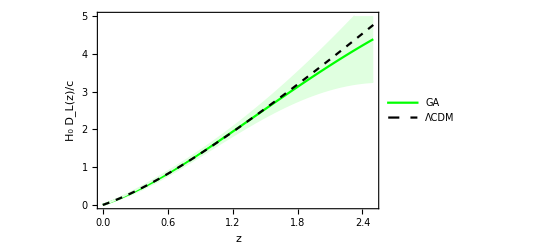

```mathematica
pltdL=Plot[{dLGA[z]+ϵ0 δdL[z,a1,a2,a3,0]/.fmindLerr[[2]]//Evaluate,DLcpl[z,ombfPanth,-1,0,1,1]/cH0},{z,0,2.5},PlotStyle->{LightGreen,Green,LightGreen,{Dashed,Black}},Filling->{1->{{3},LightGreen}},Frame->True,FrameLabel->{"z","H_0 D_L(z)/c"},FrameStyle->Black,BaseStyle->FontSize->16,PlotRange->{0,5},PlotLegends->Placed[LineLegend[{Green,{Dashed,Black}},{"GA","ΛCDM"}],Scaled[{0.8,0.2}]],Axes->None]
```

```mathematica
Export[NotebookDirectory[]<>"dLplot.pdf",pltdL,ImageResolution->600];
```

#### d_A (z) Plot

```mathematica
dAGA[x_]:=dLGA[x]/(1+x)^2;
```

```mathematica
Clear[a1,a2,a3]
(*δdL[z_,a1_,a2_,a3_]:=z^2(a1+a2 z+a3 z^2)*)
δdA[z_,a1_,a2_,a3_]:=δdL[z,a1,a2,a3,0]/(1+z)^2
```

```mathematica
b1=fminerrHtot2[[2,1,2]];
b2=fminerrHtot2[[2,2,2]];
b3=0;
b4=0;
```

```mathematica
FindMinimum[chi2baoGA[rs,HGA[x],dAGA[x],H0GA/100],{rs,rsfid,1.01 rsfid}]
rsGA=rs/.%[[2]]
```

{7770.24,{rs→111.694}}

111.694

```mathematica
(* 6dFGs and WiggleZ BAO data, see 1605.02702 *)
chi2conf6dFWig[rs_?NumericQ,a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=Module[{δfj,fbfj,vec1,vec2,conf,Dij,yj},
yj=databao6dFWig[[All,2]];
Dij=-CholeskyDecomposition[(Cijbaoinv6dFWig+Transpose[Cijbaoinv6dFWig])/2];
fbfj=Table[rs/DvGA[databao6dFWig[[i,1]],HGA[databao6dFWig[[i,1]]],dAGA[databao6dFWig[[i,1]]],1],{i,1,Length[databao6dFWig]}];
δfj=Table[-(2fbfj[[j]])/(3 dAGA[databao6dFWig[[j,1]]])δdA[databao6dFWig[[j,1]],a1,a2,a3]+1/3(fbfj[[j]]dH[databao6dFWig[[j,1]],b1,b2,b3,b4])/HGA[databao6dFWig[[j,1]]],{j,1,Length[databao6dFWig]}];
vec1=-Dij.(+yj-fbfj+δfj);
vec2=-Dij.(-yj+fbfj+δfj);
conf=Table[1/2 (Erf[vec1[[i]]/(√2) ]+Erf[vec2[[i]]/(√2) ]),{i,1,Length[databao6dFWig]}];
Sum[(conf[[k]]-Erf[1/(√2)])^2,{k,1,Length[databao6dFWig]}]]
```

```mathematica
chi2confMGSELG[rs_?NumericQ,a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=Module[{CI,yj,fbfj,δfj},
yj=dataMGSELG[[All,2]];
fbfj=Table[1/rs DvGA[dataMGSELG[[i,1]],HGA[dataMGSELG[[i,1]]],dAGA[dataMGSELG[[i,1]]],1],{i,1,Length[dataMGSELG]}];
δfj=Table[(2fbfj[[j]])/(3 dAGA[dataMGSELG[[j,1]]])δdA[dataMGSELG[[j,1]],a1,a2,a3]-1/3(fbfj[[j]]dH[dataMGSELG[[j,1]],b1,b2,b3,b4])/HGA[dataMGSELG[[j,1]]],{j,1,Length[dataMGSELG]}];CI=Table[1/2 (Erf[(δfj[[i]]+fbfj[[i]]-yj[[i]])/(√2 dataMGSELG[[i,3]])]+Erf[(δfj[[i]]-fbfj[[i]]+yj[[i]])/(√2 dataMGSELG[[i,3]])]),{i,1,Length[dataMGSELG]}];
Sum[(CI[[i]]-Erf[1/(√2)])^2,{i,1,Length[dataMGSELG]}]]
```

```mathematica
chi2confDES[rs_?NumericQ,a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=Module[{CI,yj,fbfj,δfj},
yj=dataDES3[[1,2]];
fbfj=(cH0  dAGA[dataDES3[[1,1]]])/rs;δfj=(cH0 δdA[dataDES3[[1,1]],a1,a2,a3])/rs;CI=1/2 (Erf[(δfj+fbfj-yj)/(√2 dataDES3[[1,3]])]+Erf[(δfj-fbfj+yj)/(√2 dataDES3[[1,3]])]);
(CI-Erf[1/(√2)])^2]
```

```mathematica
chi2confLya[rs_?NumericQ,a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=Module[{δfj,fbfj,vec1,vec2,conf,Dij,yj},
yj=dataLya[[All,2]];
Dij=-CholeskyDecomposition[(CijLyainv+Transpose[CijLyainv])/2];
fbfj={DHGA[HGA[dataLya[[2,1]]],1]/rs,DMGA[dataLya[[1,1]],dAGA[dataLya[[1,1]]],1,rs]};
δfj={-(fbfj[[2]]dH[dataLya[[2,1]],b1,b2,b3,b4])/HGA[dataLya[[2,1]]],(fbfj[[1]]δdA[dataLya[[1,1]],a1,a2,a3])/dAGA[dataLya[[1,1]]]};
vec1=-Dij.(+yj-fbfj+δfj);
vec2=-Dij.(-yj+fbfj+δfj);
conf=Table[1/2 (Erf[vec1[[i]]/(√2) ]+Erf[vec2[[i]]/(√2) ]),{i,1,Length[dataLya]}];
Sum[(conf[[k]]-Erf[1/(√2)])^2,{k,1,Length[dataLya]}]]
```

```mathematica
chi2confDR12[rs_?NumericQ,a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=Module[{δfj,fbfj,vec1,vec2,conf,Dij,yj},
yj=dataDR12[[All,2]];
Dij=-CholeskyDecomposition[(dataDR12Cijinv+Transpose[dataDR12Cijinv])/2];
fbfj={DMGA[dataDR12[[1,1]],dAGA[dataDR12[[1,1]]],1,rs],DHGA[HGA[dataDR12[[2,1]]],1]/rs,DMGA[dataDR12[[3,1]],dAGA[dataDR12[[3,1]]],1,rs],DHGA[HGA[dataDR12[[4,1]]],1]/rs};
δfj={(fbfj[[1]]δdA[dataDR12[[1,1]],a1,a2,a3])/dAGA[dataDR12[[1,1]]],-(fbfj[[2]]dH[dataDR12[[2,1]],b1,b2,b3,b4])/HGA[dataDR12[[2,1]]],(fbfj[[3]]δdA[dataDR12[[3,1]],a1,a2,a3])/dAGA[dataDR12[[3,1]]],-(fbfj[[4]]dH[dataDR12[[4,1]],b1,b2,b3,b4])/HGA[dataDR12[[4,1]]]};
vec1=-Dij.(+yj-fbfj+δfj);
vec2=-Dij.(-yj+fbfj+δfj);
conf=Table[1/2 (Erf[vec1[[i]]/(√2) ]+Erf[vec2[[i]]/(√2) ]),{i,1,Length[dataDR12]}];
Sum[(conf[[k]]-Erf[1/(√2)])^2,{k,1,Length[dataDR12]}]]
```

```mathematica
chi2confLRG[rs_?NumericQ,a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=Module[{δfj,fbfj,vec1,vec2,conf,Dij,yj},
yj=dataLRG[[All,2]];
Dij=-CholeskyDecomposition[(dataLRGCijinv+Transpose[dataLRGCijinv])/2];
fbfj={DMGA[dataLRG[[1,1]],dAGA[dataLRG[[1,1]]],1,rs],DHGA[HGA[dataLRG[[2,1]]],1]/rs};
δfj={(fbfj[[1]]δdA[dataLRG[[1,1]],a1,a2,a3])/dAGA[dataLRG[[1,1]]],-(fbfj[[2]]dH[dataLRG[[2,1]],b1,b2,b3,b4])/HGA[dataLRG[[2,1]]]};
vec1=-Dij.(+yj-fbfj+δfj);
vec2=-Dij.(-yj+fbfj+δfj);
conf=Table[1/2 (Erf[vec1[[i]]/(√2) ]+Erf[vec2[[i]]/(√2) ]),{i,1,Length[dataLRG]}];
Sum[(conf[[k]]-Erf[1/(√2)])^2,{k,1,Length[dataLRG]}]]
```

```mathematica
chi2confQSO[rs_?NumericQ,a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=Module[{δfj,fbfj,vec1,vec2,conf,Dij,yj},
yj=dataQSO[[All,2]];
Dij=-CholeskyDecomposition[(dataQSOCijinv+Transpose[dataQSOCijinv])/2];
fbfj={DMGA[dataQSO[[1,1]],dAGA[dataQSO[[1,1]]],1,rs],DHGA[HGA[dataQSO[[2,1]]],1]/rs};
δfj={(fbfj[[1]]δdA[dataQSO[[1,1]],a1,a2,a3])/dAGA[dataQSO[[1,1]]],-(fbfj[[2]]dH[dataQSO[[2,1]],b1,b2,b3,b4])/HGA[dataQSO[[2,1]]]};
vec1=-Dij.(+yj-fbfj+δfj);
vec2=-Dij.(-yj+fbfj+δfj);
conf=Table[1/2 (Erf[vec1[[i]]/(√2) ]+Erf[vec2[[i]]/(√2) ]),{i,1,Length[dataQSO]}];
Sum[(conf[[k]]-Erf[1/(√2)])^2,{k,1,Length[dataQSO]}]]
```

```mathematica
(* Total BAO chi^2 *)
chi2baoCI[rs_?NumericQ,a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=chi2conf6dFWig[rs,a1,a2,a3]+chi2confMGSELG[rs,a1,a2,a3]+chi2confDES[rs,a1,a2,a3]+chi2confLRG[rs,a1,a2,a3]+chi2confQSO[rs,a1,a2,a3]+chi2confLya[rs,a1,a2,a3]+chi2confDR12[rs,a1,a2,a3]
```

```mathematica
chi2baotot[rs_?NumericQ,a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=chi2baoCI[rs,a1,a2,a3]+chi2baoGA[rs,HGA[x]+dH[x,b1,b2,b3,b4],dAGA[x]+δdA[x,a1,a2,a3],H0GA/100]
```

```mathematica
chi2baotot[rsGA, 0.01,0.01,0]
```

7837.85

```mathematica
fminBAOerr=FindMinimum[chi2baotot[rsGA,a1,0,0],{a1,0.01,0.011}]
```

{7384.98,{a1→-0.241408}}

```mathematica
fminBAOerr={7384.9829945633,{a1->-0.24140773392893586}};
```

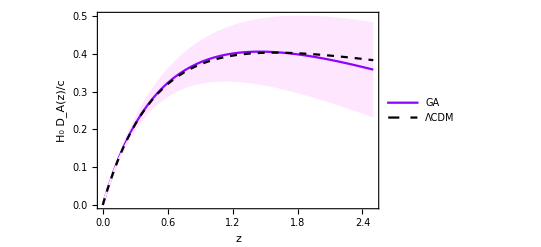

```mathematica
dAplt=Plot[{dAGA[z]+ϵ0 δdA[z,a1,0,0]/.fminBAOerr[[2]]//Evaluate,DAcpl[z,ompl,-1,0,1,1]/cH0},{z,0,2.5},PlotStyle->{LightMagenta,RGBColor["#8c04fc"],LightMagenta,{Dashed,Black}},Filling->{1->{{3},LightMagenta}},Frame->True,FrameLabel->{"z","H_0 D_A(z)/c"},FrameStyle->Black,BaseStyle->FontSize->16,PlotRange->{0,0.5},PlotLegends->Placed[LineLegend[{RGBColor["#8c04fc"],{Dashed,Black}},{"GA","ΛCDM"}],Scaled[{0.8,0.2}]],Axes->None]
```

```mathematica
Export[NotebookDirectory[]<>"daplot.pdf",dAplt,ImageResolution->600];
```